## Soliton density profile (analytic)

### 1. leapfrog with ChplUltra units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc {rho0, rc} = {27492.260803351877, 0.05359134269304645}

#### import coordinates

```mathematica
bp7pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",1;;10,6;;7}];
bp7pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",11;;20,6;;7}];
bp7pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",91;;100,6;;7}];
bp7pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",191;;200,6;;7}];
bp7pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",291;;300,6;;7}];
bp7pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",991;;1000,6;;7}];
bp7pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",1991;;2000,6;;7}];
bp7pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",2991;;3000,6;;7}];
bp7pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",3991;;4000,6;;7}];
bp7pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",4991;;5000,6;;7}];
bp7pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",5991;;6000,6;;7}];
bp7pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",6991;;7000,6;;7}];
bp7pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",7991;;8000,6;;7}];
bp7pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",8991;;9000,6;;7}];
bp7pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",9991;;10000,6;;7}];
bp7pos1500= Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",14991;;15000,6;;7}];
bp7pos2000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",19991;;20000,6;;7}];
bp7pos2085 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",20841;;20850,6;;7}];
bp7pos2086 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",20851;;20860,6;;7}];
bp7pos2087 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",20861;;20870,6;;7}];
bp7pos2500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp7.csv",{"Data",24991;;25000,6;;7}];
```

#### position

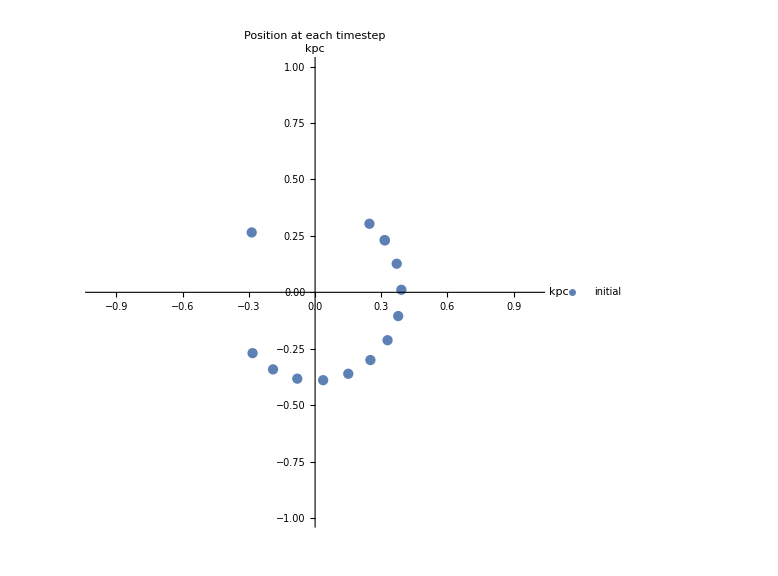

```mathematica
bp7posgraph = ListPlot[{bp7pos1[[1]],bp7pos100[[1]],bp7pos200[[1]],bp7pos300[[1]],bp7pos400[[1]],bp7pos500[[1]],bp7pos600[[1]],bp7pos700[[1]],bp7pos800[[1]],bp7pos900[[1]],bp7pos1000[[1]],bp7pos1500[[1]],bp7pos2000[[1]],bp7pos2085[[1]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

dt = 0.0479446 % of period; period = 2085.74 timesteps

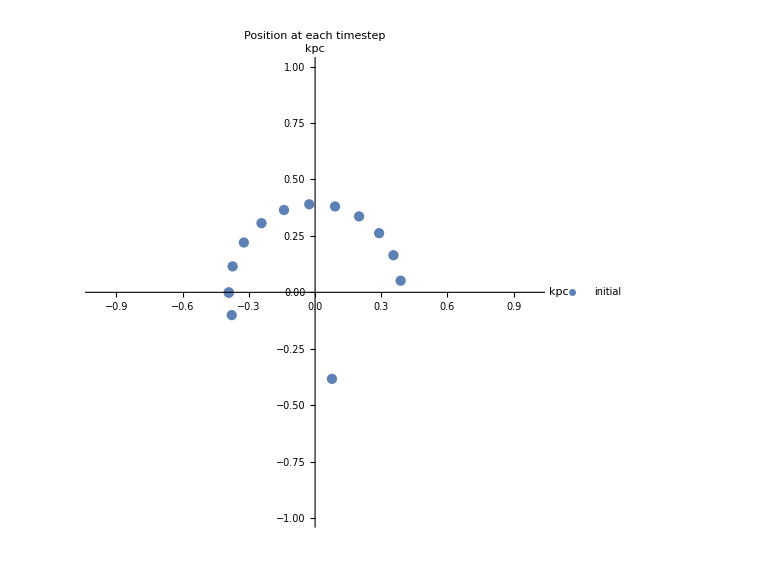

```mathematica
bp7pos5graph = ListPlot[{bp7pos1[[5]],bp7pos100[[5]],bp7pos200[[5]],bp7pos300[[5]],bp7pos400[[5]],bp7pos500[[5]],bp7pos600[[5]],bp7pos700[[5]],bp7pos800[[5]],bp7pos900[[5]],bp7pos1000[[5]],bp7pos1500[[5]],bp7pos2000[[5]],bp7pos2085[[5]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

### 2. leapfrog with ChplUltra units 1 test particles, 100,000 timesteps of 1 Myr each r0 = 15 kpc {rho0, rc} = {(0.5**4) * 27492.260803351877, 2.0*0.05359134269304645}

#### import coordinates

```mathematica
bp8pos = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp15.csv",{"Data",30000;;60000,6;;7}];
```

#### Position

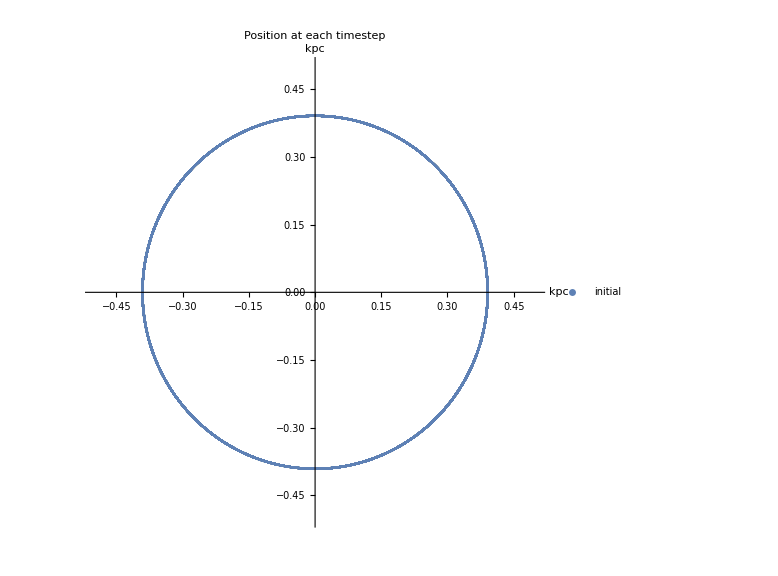

```mathematica
bp8posgraph = ListPlot[{bp8pos},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

## Soliton (imported)

#### 1. leapfrog with ChplUltra units 1 test particles, 100,000 timesteps of 1 Myr each r0 = 15 kpc 1 period ~ 22,300 timesteps

#### Import coordinates

```mathematica
bp9posxy = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv",{"Data",1;;44300,6;;7}];
bp9posyz = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv",{"Data",70000;;100000,7;;8}];
bp9period1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv",{"Data",1;;22300,6;;7}];
bp9period2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv",{"Data",22300;;44600,6;;7}];
bp9period3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv",{"Data",44600;;66950,6;;7}];
bp9period4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv",{"Data",66950;;89000,6;;7}];
bp9period5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp16.csv",{"Data",89500;;100000,6;;7}];
```

#### Position

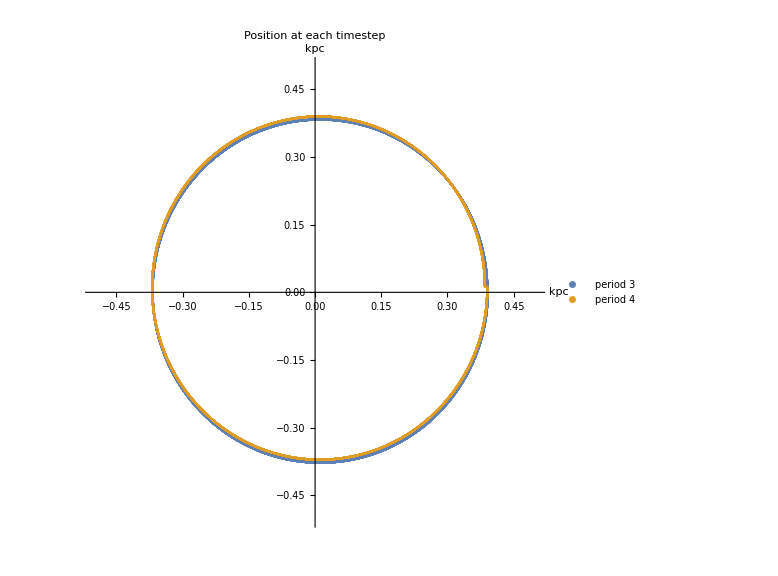

```mathematica
bp9posxy7graph = ListPlot[{bp9period1,bp9period2},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"period 3","period 4"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

After first period bottom intersection with y axis both shift up, and left intersection with x axis is shifted right compared to analytic soliton. 
Second period, bottom intersection shifted up, top intersection shifted up, right intersection shifted left. circle looks shifted up compared to first period.
Third period, bottom intersection shifts up, and top intersection shifts up, left intersection shifts left, and right intersection shifts left. circle looks shifted up and left compared to second period.
Fourth period, left and right intersections both shift left, but top and bottom intersections shift down, maybe because circle is so far to the left? Circle looks shifted left.
Fifth period, left and right intersections both shift left. bottom intersection seems shifted down 



Is the shape remaining a circle or is it becoming more oval?

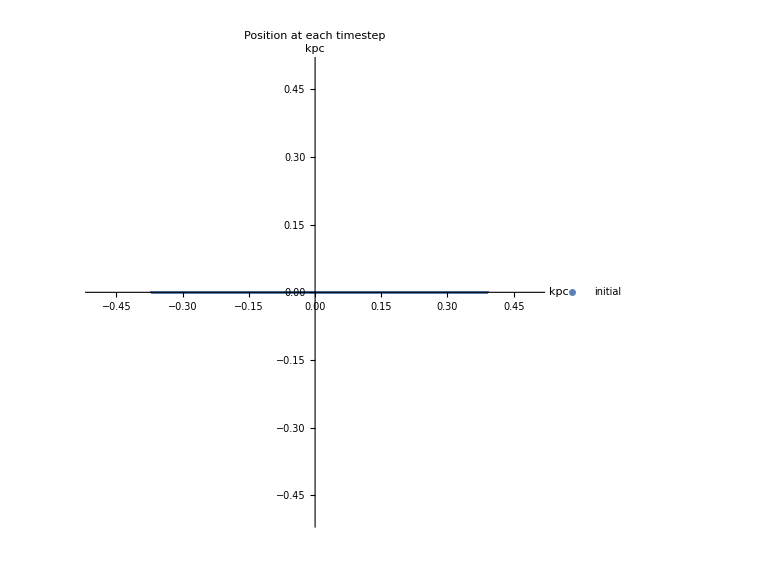

```mathematica
bp9posyzgraph = ListPlot[{bp9posyz},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

### 2. leapfrog with ChplUltra units, center shifted right 1 test particles, 100,000 timesteps of 1 Myr each r0 = 15 kpc

#### Import coordinates

```mathematica
bp10posxy = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp17.csv",{"Data",30000;;60000,6;;7}];
bp10period1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp17.csv",{"Data",1;;22300,6;;7}];
bp10period2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp17.csv",{"Data",22300;;44600,6;;7}];
bp10period3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp17.csv",{"Data",44600;;66950,6;;7}];
bp10period4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp17.csv",{"Data",66950;;89000,6;;7}];
bp10period5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp17.csv",{"Data",89500;;100000,6;;7}];
```

#### Position

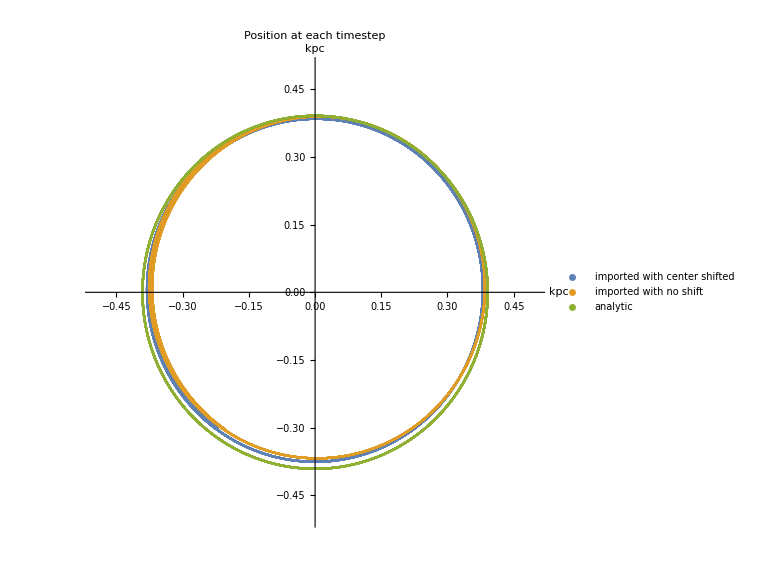

```mathematica
bp10posxygraph = ListPlot[{bp10posxy,bp9posxy,bp8pos},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"imported with center shifted","imported with no shift","analytic"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

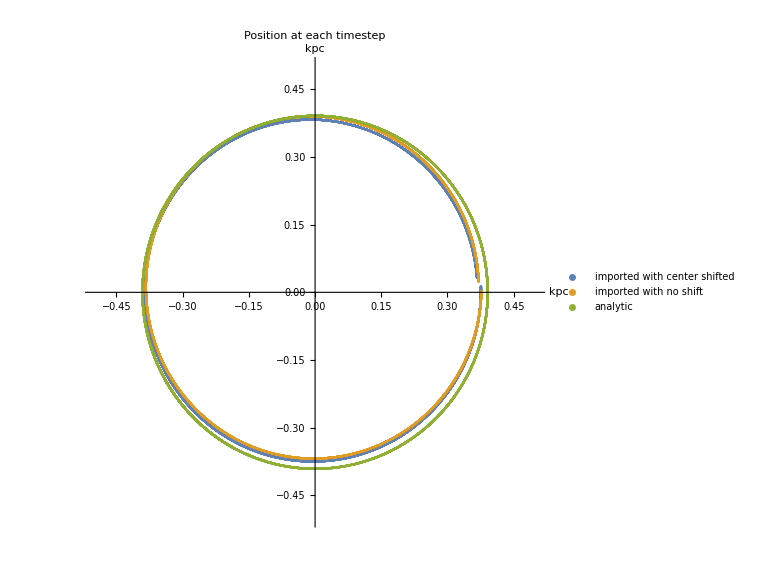

```mathematica
bp10posgraph = ListPlot[{bp10period4,bp9period4,bp8pos},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"imported with center shifted","imported with no shift","analytic"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

Shifting center appears to center circle more, but force is still consistently larger than analytic as circle is  consistently smaller.

### 3. leapfrog with ChplUltra units, center shifted right and down 1 test particles, 100,000 timesteps of 1 Myr each r0 = 15 kpc

#### Import coordinates

```mathematica
bp11posxy = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp18.csv",{"Data",1;;100000,6;;7}];
bp11period1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp18.csv",{"Data",1;;22300,6;;7}];
bp11period2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp18.csv",{"Data",22300;;44600,6;;7}];
bp11period3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp18.csv",{"Data",44600;;66950,6;;7}];
bp11period4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp18.csv",{"Data",66950;;89000,6;;7}];
bp11period5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp18.csv",{"Data",89500;;100000,6;;7}];
```

#### Position

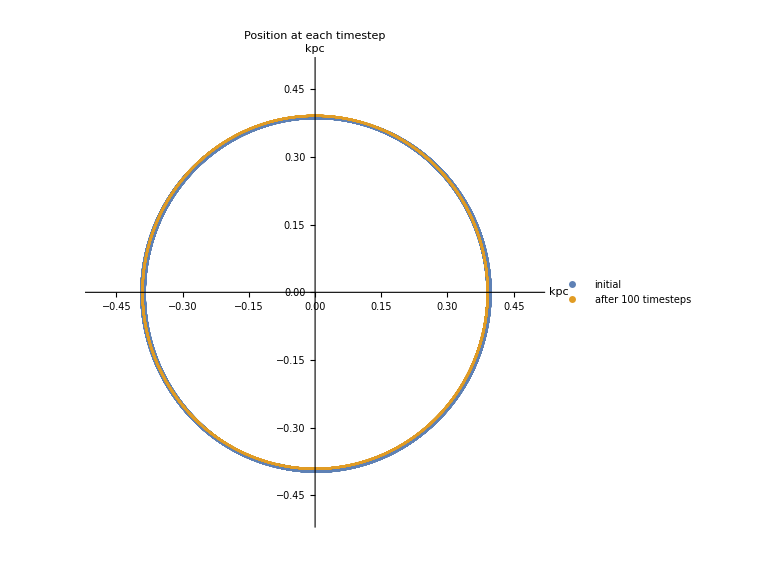

```mathematica
bp11posxygraph = ListPlot[{bp11posxy,bp8pos},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

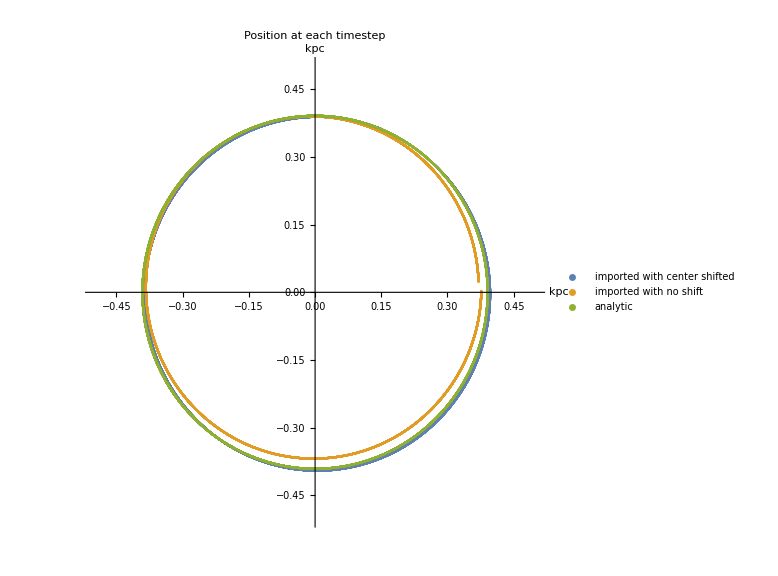

```mathematica
bp11posgraph = ListPlot[{bp11period4,bp9period4, bp8pos},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"imported with center shifted","imported with no shift","analytic"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

path seems much more accurate. Significant smallness compared to analytic is gone; now path is even slightly larger than that of analytic? This difference becomes clearer by the third period as the circle shifts down compared to the analytic. Remove less?

### 4. leapfrog with ChplUltra units, center shifted right 1/2 a gridpoint and down 3/8 of a gridpoint 1 test particles, 100,000 timesteps of 1 Myr each r0 = 15 kpc

#### Import coordinates

```mathematica
bp12posxy = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",1;;100000,6;;7}];
bp12period1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",1;;22300,6;;7}];
bp12period2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",22300;;44600,6;;7}];
bp12period3 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",44600;;66950,6;;7}];
bp12period4 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",66950;;89000,6;;7}];
bp12period5 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp19.csv",{"Data",89500;;100000,6;;7}];
```

#### Position

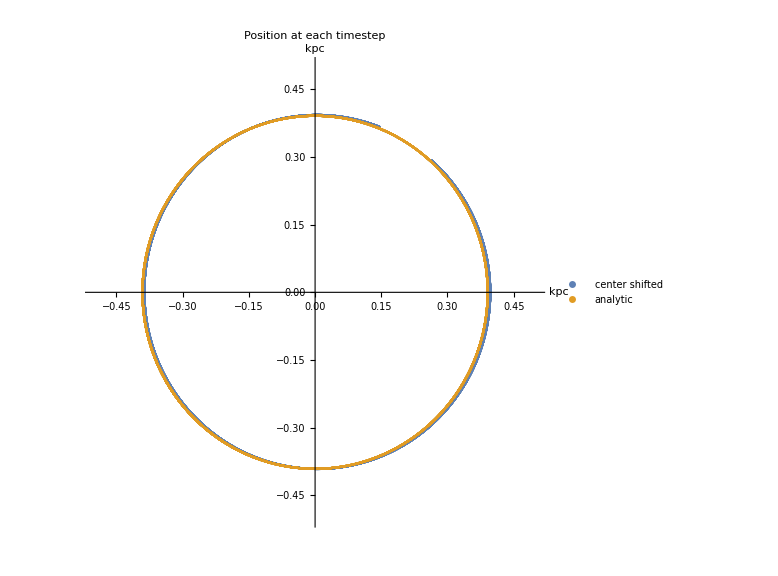

```mathematica
bp12posxygraph = ListPlot[{bp12period4,bp8pos},PlotRange->{{-0.5,0.5},{-0.5,0.5}},AspectRatio->1,ImageSize->Large,PlotLegends->{"center shifted","analytic"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

center shifted right 3/4 a gridpoint is way too much to the right.
shifting center down 3/8 of a gridpoint is better than shifting down just 1/4.
shifting center right 5/8 of a gridpoint is immediately way more off than 1/2.

## Comparison

#### Analytic #2 v imported #1

```mathematica
Differences[{bp9pos,bp8pos}]
```

{{{0.,0.},{0.,0.},{0.,-1.×10^-9},{0.,-2.×10^-9},{0.,-4.×10^-9},{0.,-7.×10^-9},{0.,-1.×10^-8},{0.,-1.2×10^-8},{0.,-1.6×10^-8},{0.,-2.1×10^-8},{0.,-3.×10^-8},{0.,-3.×10^-8},{0.,-4.×10^-8},{0.,-4.×10^-8},{0.,-5.×10^-8},{0.,-6.×10^-8},{0.,-6.×10^-8},{0.,-8.×10^-8},{0.,-8.×10^-8},{0.,-9.×10^-8},{0.,-1.×10^-7},{0.,-1.×10^-7},{-1.×10^-6,-1.2×10^-7},{0.,-1.2×10^-7},{0.,-1.4×10^-7},{-1.×10^-6,-1.5×10^-7},{0.,-1.6×10^-7},{0.,-1.7×10^-7},{0.,-1.8×10^-7},{-1.×10^-6,-1.9×10^-7},{0.,-2.1×10^-7},{0.,-2.2×10^-7},{0.,-2.3×10^-7},{0.,-2.4×10^-7},{0.,-2.6×10^-7},{0.,-2.8×10^-7},{0.,-2.9×10^-7},{0.,-3.1×10^-7},{0.,-3.2×10^-7},{0.,-3.3×10^-7},{0.,-3.5×10^-7},{0.,-3.7×10^-7},{0.,-3.8×10^-7},{-1.×10^-6,-4.×10^-7},{-1.×10^-6,-4.2×10^-7},{0.,-4.3×10^-7},{0.,-4.4×10^-7},{0.,-4.6×10^-7},{-1.×10^-6,-4.8×10^-7},{0.,-5.×10^-7},{-1.×10^-6,-5.1×10^-7},{-1.×10^-6,-5.3×10^-7},{0.,-5.5×10^-7},{-1.×10^-6,-5.7×10^-7},{0.,-5.9×10^-7},{-1.×10^-6,-6.×10^-7},{0.,-6.3×10^-7},{-1.×10^-6,-6.4×10^-7},{-1.×10^-6,-6.6×10^-7},{0.,-6.8×10^-7},{-1.×10^-6,-7.×10^-7},{0.,-7.1×10^-7},{0.,-7.4×10^-7},{-1.×10^-6,-7.6×10^-7},{-1.×10^-6,-7.7×10^-7},{0.,-7.9×10^-7},{0.,-8.1×10^-7},{-1.×10^-6,-8.3×10^-7},{-1.×10^-6,-8.5×10^-7},{-1.×10^-6,-8.7×10^-7},{-1.×10^-6,-8.9×10^-7},{-1.×10^-6,-9.1×10^-7},{-1.×10^-6,-9.3×10^-7},{-1.×10^-6,-9.5×10^-7},{-1.×10^-6,-9.6×10^-7},{-1.×10^-6,-9.9×10^-7},{-1.×10^-6,-1.×10^-6},{-1.×10^-6,-1.03×10^-6},{-1.×10^-6,-1.04×10^-6},{-1.×10^-6,-1.06×10^-6},{-1.×10^-6,-1.09×10^-6},{-1.×10^-6,-1.1×10^-6},{-1.×10^-6,-1.12×10^-6},{-1.×10^-6,-1.14×10^-6},{-1.×10^-6,-1.16×10^-6},{-1.×10^-6,-1.18×10^-6},{-1.×10^-6,-1.2×10^-6},{-1.×10^-6,-1.22×10^-6},{-1.×10^-6,-1.24×10^-6},{-2.×10^-6,-1.25×10^-6},{-1.×10^-6,-1.27×10^-6},{-2.×10^-6,-1.29×10^-6},{-1.×10^-6,-1.31×10^-6},{-2.×10^-6,-1.32×10^-6},{-1.×10^-6,-1.34×10^-6},{-1.×10^-6,-1.36×10^-6},{-2.×10^-6,-1.37×10^-6},{-1.×10^-6,-1.4×10^-6},{-2.×10^-6,-1.4×10^-6},{-2.×10^-6,-1.4×10^-6},{-2.×10^-6,-1.5×10^-6},{-1.×10^-6,-1.5×10^-6},{-2.×10^-6,-1.5×10^-6},{-2.×10^-6,-1.4×10^-6},{-2.×10^-6,-1.5×10^-6},{-2.×10^-6,-1.5×10^-6},{-2.×10^-6,-1.5×10^-6},{-2.×10^-6,-1.6×10^-6},{-2.×10^-6,-1.6×10^-6},{-2.×10^-6,-1.6×10^-6},{-2.×10^-6,-1.6×10^-6},{-2.×10^-6,-1.6×10^-6},{-2.×10^-6,-1.7×10^-6},{-2.×10^-6,-1.7×10^-6},{-2.×10^-6,-1.7×10^-6},{-2.×10^-6,-1.7×10^-6},{-3.×10^-6,-1.7×10^-6},{-3.×10^-6,-1.6×10^-6},{-2.×10^-6,-1.7×10^-6},{-2.×10^-6,-1.7×10^-6},{-3.×10^-6,-1.7×10^-6},{-2.×10^-6,-1.7×10^-6},{-2.×10^-6,-1.7×10^-6},{-3.×10^-6,-1.7×10^-6},{-2.×10^-6,-1.7×10^-6},{-3.×10^-6,-1.7×10^-6},{-3.×10^-6,-1.7×10^-6},{-3.×10^-6,-1.8×10^-6},{-3.×10^-6,-1.8×10^-6},{-3.×10^-6,-1.8×10^-6},{-3.×10^-6,-1.8×10^-6},{-3.×10^-6,-1.9×10^-6},{-3.×10^-6,-1.9×10^-6},{-3.×10^-6,-1.9×10^-6},{-3.×10^-6,-1.9×10^-6},{-3.×10^-6,-1.9×10^-6},{-3.×10^-6,-1.9×10^-6},{-3.×10^-6,-1.9×10^-6},{-3.×10^-6,-1.9×10^-6},{-3.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.8×10^-6},{-4.×10^-6,-1.8×10^-6},{-4.×10^-6,-1.8×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.8×10^-6},{-4.×10^-6,-1.8×10^-6},{-3.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.8×10^-6},{-4.×10^-6,-1.8×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.8×10^-6},{-4.×10^-6,-1.8×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.8×10^-6},{-5.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.8×10^-6},{-5.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-4.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-6.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-5.×10^-6,-1.9×10^-6},{-5.×10^-6,-2.×10^-6},{-5.×10^-6,-1.9×10^-6},{-5.×10^-6,-2.×10^-6},{-5.×10^-6,-2.×10^-6},{-5.×10^-6,-2.×10^-6},{-6.×10^-6,-2.×10^-6},{-6.×10^-6,-2.×10^-6},{-6.×10^-6,-2.1×10^-6},{-5.×10^-6,-2.×10^-6},{-5.×10^-6,-2.1×10^-6},{-6.×10^-6,-2.1×10^-6},{-6.×10^-6,-2.1×10^-6},{-5.×10^-6,-2.1×10^-6},{-6.×10^-6,-2.2×10^-6},{-6.×10^-6,-2.1×10^-6},{-5.×10^-6,-2.1×10^-6},{-6.×10^-6,-2.2×10^-6},{-6.×10^-6,-2.2×10^-6},{-6.×10^-6,-2.2×10^-6},{-6.×10^-6,-2.2×10^-6},{-6.×10^-6,-2.2×10^-6},{-6.×10^-6,-2.3×10^-6},{-6.×10^-6,-2.3×10^-6},{-5.×10^-6,-2.3×10^-6},{-6.×10^-6,-2.3×10^-6},{-6.×10^-6,-2.3×10^-6},{-5.×10^-6,-2.3×10^-6},{-6.×10^-6,-2.3×10^-6},{-6.×10^-6,-2.4×10^-6},{-6.×10^-6,-2.4×10^-6},{-6.×10^-6,-2.4×10^-6},{-5.×10^-6,-2.4×10^-6},{-6.×10^-6,-2.4×10^-6},{-6.×10^-6,-2.5×10^-6},{-6.×10^-6,-2.5×10^-6},{-6.×10^-6,-2.5×10^-6},{-6.×10^-6,-2.5×10^-6},{-6.×10^-6,-2.6×10^-6},{-6.×10^-6,-2.6×10^-6},{-6.×10^-6,-2.6×10^-6},{-5.×10^-6,-2.7×10^-6},{-5.×10^-6,-2.7×10^-6},{-5.×10^-6,-2.7×10^-6},{-6.×10^-6,-2.8×10^-6},{-6.×10^-6,-2.7×10^-6},{-5.×10^-6,-2.8×10^-6},{-5.×10^-6,-2.8×10^-6},{-6.×10^-6,-2.9×10^-6},{-5.×10^-6,-2.8×10^-6},{-5.×10^-6,-2.9×10^-6},{-6.×10^-6,-2.9×10^-6},{-5.×10^-6,-3.×10^-6},{-5.×10^-6,-2.9×10^-6},{-5.×10^-6,-3.×10^-6},{-5.×10^-6,-3.×10^-6},{-5.×10^-6,-3.×10^-6},{-5.×10^-6,-3.1×10^-6},{-5.×10^-6,-3.×10^-6},{-4.×10^-6,-3.1×10^-6},{-5.×10^-6,-3.2×10^-6},{-5.×10^-6,-3.1×10^-6},{-4.×10^-6,-3.2×10^-6},{-4.×10^-6,-3.2×10^-6},{-5.×10^-6,-3.2×10^-6},{-5.×10^-6,-3.2×10^-6},{-4.×10^-6,-3.2×10^-6},{-4.×10^-6,-3.3×10^-6},{-4.×10^-6,-3.3×10^-6},{-4.×10^-6,-3.4×10^-6},{-4.×10^-6,-3.3×10^-6},{-4.×10^-6,-3.3×10^-6},{-4.×10^-6,-3.4×10^-6},{-4.×10^-6,-3.4×10^-6},{-4.×10^-6,-3.4×10^-6},{-4.×10^-6,-3.5×10^-6},{-4.×10^-6,-3.5×10^-6},{-4.×10^-6,-3.5×10^-6},{-3.×10^-6,-3.5×10^-6},{-3.×10^-6,-3.6×10^-6},{-3.×10^-6,-3.6×10^-6},{-3.×10^-6,-3.6×10^-6},{-3.×10^-6,-3.6×10^-6},{-3.×10^-6,-3.6×10^-6},{-3.×10^-6,-3.6×10^-6},{-2.×10^-6,-3.8×10^-6},{-3.×10^-6,-3.8×10^-6},{-2.×10^-6,-3.8×10^-6},{-3.×10^-6,-3.8×10^-6},{-2.×10^-6,-3.8×10^-6},{-2.×10^-6,-3.9×10^-6},{-2.×10^-6,-3.9×10^-6},{-2.×10^-6,-3.9×10^-6},{-2.×10^-6,-3.9×10^-6},{-1.×10^-6,-4.×10^-6},{-2.×10^-6,-3.9×10^-6},{-2.×10^-6,-3.9×10^-6},{-1.×10^-6,-4.×10^-6},{-1.×10^-6,-4.×10^-6},{-1.×10^-6,-4.×10^-6},{-1.×10^-6,-4.1×10^-6},{-1.×10^-6,-4.×10^-6},{-1.×10^-6,-4.1×10^-6},{-1.×10^-6,-4.1×10^-6},{-1.×10^-6,-4.2×10^-6},{0.,-4.1×10^-6},{0.,-4.2×10^-6},{0.,-4.2×10^-6},{0.,-4.2×10^-6},{0.,-4.2×10^-6},{1.×10^-6,-4.2×10^-6},{1.×10^-6,-4.2×10^-6},{1.×10^-6,-4.2×10^-6},{1.×10^-6,-4.3×10^-6},{1.×10^-6,-4.3×10^-6},{2.×10^-6,-4.3×10^-6},{1.×10^-6,-4.3×10^-6},{1.×10^-6,-4.3×10^-6},{2.×10^-6,-4.3×10^-6},{2.×10^-6,-4.4×10^-6},{2.×10^-6,-4.4×10^-6},{2.×10^-6,-4.3×10^-6},{3.×10^-6,-4.4×10^-6},{2.×10^-6,-4.4×10^-6},{3.×10^-6,-4.4×10^-6},{3.×10^-6,-4.5×10^-6},{3.×10^-6,-4.5×10^-6},{4.×10^-6,-4.5×10^-6},{3.×10^-6,-4.5×10^-6},{4.×10^-6,-4.5×10^-6},{4.×10^-6,-4.5×10^-6},{4.×10^-6,-4.6×10^-6},{4.×10^-6,-4.6×10^-6},{4.×10^-6,-4.6×10^-6},{5.×10^-6,-4.6×10^-6},{5.×10^-6,-4.6×10^-6},{5.×10^-6,-4.7×10^-6},{6.×10^-6,-4.7×10^-6},{6.×10^-6,-4.7×10^-6},{6.×10^-6,-4.7×10^-6},{6.×10^-6,-4.8×10^-6},{6.×10^-6,-4.8×10^-6},{6.×10^-6,-4.8×10^-6},{6.×10^-6,-4.8×10^-6},{7.×10^-6,-4.8×10^-6},{7.×10^-6,-4.9×10^-6},{7.×10^-6,-4.9×10^-6},{8.×10^-6,-4.9×10^-6},{7.×10^-6,-5.×10^-6},{7.×10^-6,-5.×10^-6},{7.×10^-6,-5.×10^-6},{8.×10^-6,-5.×10^-6},{8.×10^-6,-5.1×10^-6},{9.×10^-6,-5.1×10^-6},{9.×10^-6,-5.2×10^-6},{8.×10^-6,-5.1×10^-6},{9.×10^-6,-5.2×10^-6},{9.×10^-6,-5.3×10^-6},{9.×10^-6,-5.3×10^-6},{0.00001,-5.3×10^-6},{0.00001,-5.4×10^-6},{0.00001,-5.4×10^-6},{0.00001,-5.5×10^-6},{0.00001,-5.5×10^-6},{0.000011,-5.5×10^-6},{0.000011,-5.6×10^-6},{0.000011,-5.6×10^-6},{0.000011,-5.6×10^-6},{0.000012,-5.6×10^-6},{0.000012,-5.7×10^-6},{0.000012,-5.8×10^-6},{0.000013,-5.8×10^-6},{0.000013,-5.8×10^-6},{0.000013,-5.8×10^-6},{0.000014,-5.9×10^-6},{0.000014,-5.9×10^-6},{0.000014,-6.×10^-6},{0.000014,-6.×10^-6},{0.000014,-6.×10^-6},{0.000014,-6.1×10^-6},{0.000014,-6.1×10^-6},{0.000015,-6.2×10^-6},{0.000015,-6.3×10^-6},{0.000015,-6.3×10^-6},{0.000016,-6.3×10^-6},{0.000016,-6.4×10^-6},{0.000016,-6.4×10^-6},{0.000017,-6.5×10^-6},{0.000017,-6.5×10^-6},{0.000017,-6.5×10^-6},{0.000017,-6.6×10^-6},{0.000017,-6.6×10^-6},{0.000018,-6.7×10^-6},{0.000019,-6.8×10^-6},{0.000018,-6.8×10^-6},{0.000019,-6.9×10^-6},{0.000019,-6.9×10^-6},{0.000019,-6.9×10^-6},{0.00002,-7.×10^-6},{0.00002,-7.×10^-6},{0.00002,-7.1×10^-6},{0.00002,-7.1×10^-6},{0.000021,-7.1×10^-6},{0.000021,-7.3×10^-6},{0.000022,-7.3×10^-6},{0.000022,-7.3×10^-6},{0.000022,-7.3×10^-6},{0.000023,-7.4×10^-6},{0.000023,-7.5×10^-6},{0.000023,-7.5×10^-6},{0.000024,-7.6×10^-6},{0.000024,-7.6×10^-6},{0.000024,-7.7×10^-6},{0.000024,-7.7×10^-6},{0.000024,-7.8×10^-6},{0.000025,-7.8×10^-6},{0.000025,-7.9×10^-6},{0.000025,-8.×10^-6},{0.000025,-7.9×10^-6},{0.000026,-8.×10^-6},{0.000026,-8.1×10^-6},{0.000026,-8.1×10^-6},{0.000027,-8.2×10^-6},{0.000027,-8.2×10^-6},{0.000028,-8.3×10^-6},{0.000028,-8.4×10^-6},{0.000029,-8.3×10^-6},{0.000028,-8.4×10^-6},{0.000029,-8.4×10^-6},{0.00003,-8.5×10^-6},{0.000029,-8.5×10^-6},{0.00003,-8.6×10^-6},{0.000031,-8.6×10^-6},{0.00003,-8.7×10^-6},{0.000031,-8.8×10^-6},{0.000032,-8.8×10^-6},{0.000032,-8.9×10^-6},{0.000033,-8.9×10^-6},{0.000032,-8.9×10^-6},{0.000032,-9.1×10^-6},{0.000033,-9.1×10^-6},{0.000033,-9.1×10^-6},{0.000034,-9.2×10^-6},{0.000034,-9.2×10^-6},{0.000034,-9.2×10^-6},{0.000034,-9.3×10^-6},{0.000036,-9.3×10^-6},{0.000036,-9.4×10^-6},{0.000036,-9.4×10^-6},{0.000036,-9.5×10^-6},{0.000036,-9.6×10^-6},{0.000038,-9.6×10^-6},{0.000038,-9.7×10^-6},{0.000038,-9.7×10^-6},{0.000038,-9.7×10^-6},{0.000039,-9.8×10^-6},{0.000039,-9.9×10^-6},{0.00004,-9.9×10^-6},{0.00004,-9.9×10^-6},{0.00004,-9.9×10^-6},{0.00004,-0.00001},{0.000041,-0.0000101},{0.000041,-0.0000101},{0.000042,-0.0000101},{0.000042,-0.0000102},{0.000042,-0.0000102},{0.000043,-0.0000103},{0.000044,-0.0000103},{0.000043,-0.0000103},{0.000044,-0.0000105},{0.000044,-0.0000105},{0.000045,-0.0000105},{0.000045,-0.0000105},{0.000046,-0.0000105},{0.000046,-0.0000106},{0.000047,-0.0000106},{0.000047,-0.0000108},{0.000048,-0.0000108},{0.000048,-0.0000107},{0.000048,-0.0000108},{0.000049,-0.0000109},{0.000049,-0.0000109},{0.000049,-0.000011},{0.000049,-0.0000111},{0.00005,-0.0000111},{0.000051,-0.0000111},{0.000051,-0.0000112},{0.000051,-0.0000113},{0.000052,-0.0000113},{0.000052,-0.0000114},{0.000052,-0.0000113},{0.000053,-0.0000114},{0.000053,-0.0000115},{0.000054,-0.0000116},{0.000054,-0.0000116},{0.000055,-0.0000117},{0.000055,-0.0000117},{0.000056,-0.0000117},{0.000057,-0.0000119},{0.000056,-0.0000119},{0.000057,-0.0000119},{0.000058,-0.000012},{0.000058,-0.000012},{0.000058,-0.0000122},{0.000059,-0.0000122},{0.000059,-0.0000123},{0.00006,-0.0000124},{0.00006,-0.0000124},{0.00006,-0.0000124},{0.000061,-0.0000125},{0.000061,-0.0000126},{0.000062,-0.0000126},{0.000062,-0.0000127},{0.000062,-0.0000128},{0.000063,-0.0000128},{0.000064,-0.0000129},{0.000064,-0.000013},{0.000065,-0.000013},{0.000065,-0.0000131},{0.000065,-0.0000132},{0.000066,-0.0000133},{0.000067,-0.0000133},{0.000067,-0.0000134},{0.000067,-0.0000135},{0.000068,-0.0000135},{0.000068,-0.0000136},{0.000069,-0.0000137},{0.000069,-0.0000137},{0.00007,-0.0000138},{0.00007,-0.0000138},{0.000071,-0.000014},{0.000071,-0.0000141},{0.000072,-0.0000141},{0.000072,-0.0000142},{0.000072,-0.0000143},{0.000073,-0.0000144},{0.000073,-0.0000145},{0.000074,-0.0000144},{0.000074,-0.0000145},{0.000075,-0.0000146},{0.000076,-0.0000147},{0.000075,-0.0000147},{0.000076,-0.0000149},{0.000077,-0.000015},{0.000077,-0.000015},{0.000078,-0.0000151},{0.000078,-0.0000151},{0.000079,-0.0000153},{0.000079,-0.0000153},{0.00008,-0.0000154},{0.00008,-0.0000155},{0.000081,-0.0000155},{0.000082,-0.0000157},{0.000082,-0.0000157},{0.000082,-0.0000158},{0.000083,-0.0000159},{0.000084,-0.0000159},{0.000084,-0.000016},{0.000084,-0.0000161},{0.000085,-0.0000162},{0.000085,-0.0000162},{0.000086,-0.0000163},{0.000086,-0.0000164},{0.000087,-0.0000165},{0.000087,-0.0000166},{0.000088,-0.0000167},{0.000088,-0.0000167},{0.000089,-0.0000168},{0.00009,-0.000017},{0.00009,-0.000017},{0.000091,-0.0000171},{0.000092,-0.0000171},{0.000091,-0.0000173},{0.000092,-0.0000173},{0.000093,-0.0000174},{0.000094,-0.0000175},{0.000094,-0.0000175},{0.000095,-0.0000177},{0.000094,-0.0000177},{0.000095,-0.0000178},{0.000096,-0.0000179},{0.000096,-0.0000179},{0.000097,-0.000018},{0.000097,-0.0000181},{0.000099,-0.0000182},{0.000099,-0.0000183},{0.000099,-0.0000184},{0.0001,-0.0000184},{0.0001,-0.0000185},{0.0001,-0.0000186},{0.000102,-0.0000187},{0.000102,-0.0000188},{0.000102,-0.0000189},{0.000103,-0.0000189},{0.000104,-0.000019},{0.000104,-0.000019},{0.000105,-0.0000192},{0.000105,-0.0000192},{0.000106,-0.0000194},{0.000106,-0.0000194},{0.000107,-0.0000194},{0.000108,-0.0000196},{0.000108,-0.0000197},{0.000109,-0.0000197},{0.000109,-0.0000198},{0.00011,-0.0000198},{0.000111,-0.0000199},{0.000111,-0.00002},{0.000111,-0.0000201},{0.000112,-0.0000202},{0.000113,-0.0000202},{0.000113,-0.0000203},{0.000114,-0.0000204},{0.000115,-0.0000205},{0.000115,-0.0000205},{0.000116,-0.0000206},{0.000116,-0.0000208},{0.000117,-0.0000208},{0.000118,-0.0000209},{0.000118,-0.0000209},{0.000118,-0.0000211},{0.000119,-0.0000211},{0.000119,-0.0000211},{0.000121,-0.0000213},{0.000121,-0.0000213},{0.000121,-0.0000214},{0.000122,-0.0000214},{0.000123,-0.0000216},{0.000123,-0.0000216},{0.000124,-0.0000217},{0.000125,-0.0000218},{0.000125,-0.0000219},{0.000126,-0.000022},{0.000126,-0.000022},{0.000127,-0.0000221},{0.000127,-0.0000222},{0.000128,-0.0000223},{0.000129,-0.0000223},{0.000129,-0.0000224},{0.00013,-0.0000225},{0.000131,-0.0000225},{0.000131,-0.0000227},{0.000132,-0.0000227},{0.000133,-0.0000229},{0.000133,-0.0000229},{0.000134,-0.000023},{0.000134,-0.0000231},{0.000135,-0.0000232},{0.000135,-0.0000233},{0.000136,-0.0000233},{0.000137,-0.0000234},{0.000137,-0.0000235},{0.000138,-0.0000236},{0.000138,-0.0000237},{0.000139,-0.0000238},{0.000139,-0.0000239},{0.000141,-0.000024},{0.000141,-0.0000241},{0.000142,-0.0000241},{0.000142,-0.0000243},{0.000143,-0.0000244},{0.000144,-0.0000244},{0.000144,-0.0000246},{0.000144,-0.0000246},{0.000146,-0.0000248},{0.000146,-0.0000248},{0.000147,-0.0000249},{0.000147,-0.0000251},{0.000148,-0.0000251},{0.000149,-0.0000252},{0.00015,-0.0000253},{0.00015,-0.0000254},{0.000151,-0.0000256},{0.000151,-0.0000257},{0.000152,-0.0000257},693,{0.000746,-0.000122},{0.000746,-0.000122},{0.000748,-0.000122},{0.000749,-0.000122},{0.00075,-0.000123},{0.000752,-0.000123},{0.000752,-0.000123},{0.000753,-0.000123},{0.000755,-0.000124},{0.000756,-0.000124},{0.000757,-0.000124},{0.000758,-0.000124},{0.000759,-0.000124},{0.00076,-0.000125},{0.000761,-0.000125},{0.000762,-0.000125},{0.000763,-0.000125},{0.000764,-0.000125},{0.000766,-0.000126},{0.000767,-0.000126},{0.000768,-0.000126},{0.000769,-0.000127},{0.000771,-0.000126},{0.000772,-0.000126},{0.000773,-0.000127},{0.000773,-0.000127},{0.000775,-0.000127},{0.000776,-0.000128},{0.000778,-0.000128},{0.000778,-0.000128},{0.00078,-0.000128},{0.00078,-0.000129},{0.000782,-0.000129},{0.000783,-0.000129},{0.000784,-0.000129},{0.000786,-0.000129},{0.000786,-0.00013},{0.000788,-0.00013},{0.000789,-0.00013},{0.00079,-0.00013},{0.000791,-0.00013},{0.000792,-0.00013},{0.000794,-0.00013},{0.000794,-0.000132},{0.000795,-0.000132},{0.000797,-0.000132},{0.000798,-0.000132},{0.000799,-0.000132},{0.0008,-0.000132},{0.000801,-0.000132},{0.000803,-0.000133},{0.000804,-0.000133},{0.000805,-0.000133},{0.000806,-0.000133},{0.000807,-0.000133},{0.000808,-0.000134},{0.00081,-0.000134},{0.000811,-0.000134},{0.000812,-0.000134},{0.000813,-0.000135},{0.000813,-0.000135},{0.000815,-0.000135},{0.000816,-0.000136},{0.000817,-0.000136},{0.000819,-0.000136},{0.000819,-0.000136},{0.000821,-0.000136},{0.000822,-0.000136},{0.000823,-0.000137},{0.000824,-0.000137},{0.000826,-0.000137},{0.000826,-0.000138},{0.000828,-0.000137},{0.000829,-0.000138},{0.00083,-0.000138},{0.000832,-0.000138},{0.000832,-0.000139},{0.000833,-0.000138},{0.000835,-0.000139},{0.000835,-0.000139},{0.000837,-0.00014},{0.000838,-0.000139},{0.000839,-0.00014},{0.000841,-0.00014},{0.000842,-0.00014},{0.000842,-0.00014},{0.000843,-0.000141},{0.000844,-0.00014},{0.000846,-0.000141},{0.000847,-0.000142},{0.000848,-0.000141},{0.000849,-0.000142},{0.000851,-0.000142},{0.000852,-0.000142},{0.000853,-0.000143},{0.000854,-0.000142},{0.000855,-0.000143},{0.000856,-0.000143},{0.000858,-0.000143},{0.000859,-0.000144},{0.000859,-0.000144},{0.00086,-0.000144},{0.000862,-0.000144},{0.000863,-0.000145},{0.000865,-0.000145},{0.000865,-0.000145},{0.000866,-0.000145},{0.000868,-0.000145},{0.000868,-0.000146},{0.00087,-0.000145},{0.000871,-0.000146},{0.000872,-0.000146},{0.000874,-0.000147},{0.000874,-0.000147},{0.000876,-0.000147},{0.000877,-0.000147},{0.000877,-0.000147},{0.000879,-0.000147},{0.00088,-0.000148},{0.000882,-0.000148},{0.000882,-0.000148},{0.000883,-0.000149},{0.000885,-0.000149},{0.000886,-0.000149},{0.000887,-0.000149},{0.000888,-0.000149},{0.000889,-0.000149},{0.000891,-0.000149},{0.000892,-0.00015},{0.000893,-0.00015},{0.000894,-0.00015},{0.000895,-0.00015},{0.000896,-0.00015},{0.000897,-0.000151},{0.000898,-0.000151},{0.0009,-0.000152},{0.000901,-0.000152},{0.000902,-0.000152},{0.000903,-0.000152},{0.000904,-0.000152},{0.000905,-0.000153},{0.000906,-0.000153},{0.000908,-0.000153},{0.000909,-0.000153},{0.00091,-0.000154},{0.000911,-0.000154},{0.000912,-0.000154},{0.000913,-0.000154},{0.000915,-0.000154},{0.000915,-0.000154},{0.000917,-0.000155},{0.000918,-0.000155},{0.000919,-0.000155},{0.000921,-0.000155},{0.000921,-0.000156},{0.000922,-0.000156},{0.000924,-0.000156},{0.000924,-0.000156},{0.000926,-0.000157},{0.000927,-0.000156},{0.000928,-0.000156},{0.00093,-0.000157},{0.000931,-0.000157},{0.000932,-0.000157},{0.000933,-0.000158},{0.000934,-0.000158},{0.000936,-0.000158},{0.000937,-0.000158},{0.000938,-0.000158},{0.000939,-0.000159},{0.00094,-0.000159},{0.000941,-0.000159},{0.000942,-0.000159},{0.000943,-0.00016},{0.000945,-0.00016},{0.000946,-0.00016},{0.000947,-0.00016},{0.000949,-0.000161},{0.000949,-0.000161},{0.00095,-0.000161},{0.000952,-0.000161},{0.000953,-0.000162},{0.000955,-0.000162},{0.000955,-0.000162},{0.000957,-0.000162},{0.000958,-0.000162},{0.000959,-0.000163},{0.00096,-0.000163},{0.000962,-0.000163},{0.000963,-0.000163},{0.000964,-0.000164},{0.000965,-0.000164},{0.000967,-0.000164},{0.000967,-0.000165},{0.000969,-0.000164},{0.00097,-0.000165},{0.000971,-0.000165},{0.000973,-0.000166},{0.000974,-0.000165},{0.000974,-0.000166},{0.000976,-0.000166},{0.000977,-0.000166},{0.000978,-0.000167},{0.000979,-0.000166},{0.000981,-0.000167},{0.000983,-0.000167},{0.000984,-0.000167},{0.000985,-0.000168},{0.000986,-0.000168},{0.000987,-0.000169},{0.000988,-0.000169},{0.00099,-0.000168},{0.000991,-0.000169},{0.000992,-0.000169},{0.000993,-0.000169},{0.000995,-0.000169},{0.000996,-0.00017},{0.000997,-0.00017},{0.000999,-0.00017},{0.000999,-0.00017},{0.001001,-0.000171},{0.001002,-0.000171},{0.001004,-0.000171},{0.001004,-0.000171},{0.001006,-0.000172},{0.001008,-0.000173},{0.001008,-0.000173},{0.00101,-0.000173},{0.001011,-0.000173},{0.001012,-0.000173},{0.001014,-0.000173},{0.001015,-0.000173},{0.001016,-0.000175},{0.001017,-0.000175},{0.001018,-0.000175},{0.00102,-0.000175},{0.001021,-0.000176},{0.001023,-0.000176},{0.001024,-0.000176},{0.001025,-0.000176},{0.001026,-0.000177},{0.001028,-0.000177},{0.001029,-0.000177},{0.00103,-0.000177},{0.001031,-0.000178},{0.001032,-0.000178},{0.001034,-0.000178},{0.001035,-0.000179},{0.001036,-0.000178},{0.001038,-0.000179},{0.001039,-0.000179},{0.00104,-0.000179},{0.001042,-0.00018},{0.001043,-0.00018},{0.001044,-0.000181},{0.001046,-0.00018},{0.001046,-0.000181},{0.001047,-0.000181},{0.001049,-0.000182},{0.00105,-0.000182},{0.001052,-0.000182},{0.001052,-0.000182},{0.001054,-0.000183},{0.001056,-0.000183},{0.001056,-0.000183},{0.001058,-0.000183},{0.00106,-0.000184},{0.00106,-0.000185},{0.001062,-0.000184},{0.001063,-0.000185},{0.001064,-0.000186},{0.001065,-0.000185},{0.001067,-0.000186},{0.001068,-0.000186},{0.00107,-0.000186},{0.001071,-0.000187},{0.001073,-0.000187},{0.001074,-0.000187},{0.001075,-0.000187},{0.001076,-0.000188},{0.001078,-0.000188},{0.001079,-0.000188},{0.00108,-0.000188},{0.001081,-0.000189},{0.001083,-0.000189},{0.001084,-0.00019},{0.001085,-0.000189},{0.001087,-0.00019},{0.001088,-0.00019},{0.001089,-0.000191},{0.00109,-0.000191},{0.001092,-0.000192},{0.001093,-0.000192},{0.001095,-0.000192},{0.001096,-0.000193},{0.001097,-0.000193},{0.001099,-0.000193},{0.001099,-0.000193},{0.001101,-0.000193},{0.001102,-0.000193},{0.001104,-0.000194},{0.001105,-0.000194},{0.001106,-0.000194},{0.001108,-0.000196},{0.001109,-0.000196},{0.00111,-0.000196},{0.001112,-0.000196},{0.001113,-0.000197},{0.001114,-0.000197},{0.001116,-0.000197},{0.001117,-0.000197},{0.001119,-0.000197},{0.00112,-0.000198},{0.001121,-0.000199},{0.001122,-0.000199},{0.001123,-0.000199},{0.001125,-0.000199},{0.001126,-0.000199},{0.001127,-0.0002},{0.001128,-0.0002},{0.001131,-0.0002},{0.001132,-0.0002},{0.001133,-0.000202},{0.001134,-0.000202},{0.001136,-0.000202},{0.001137,-0.000203},{0.001139,-0.000203},{0.00114,-0.000203},{0.001141,-0.000204},{0.001142,-0.000204},{0.001144,-0.000203},{0.001145,-0.000204},{0.001147,-0.000204},{0.001148,-0.000204},{0.001149,-0.000205},{0.001151,-0.000205},{0.001152,-0.000206},{0.001153,-0.000206},{0.001154,-0.000207},{0.001156,-0.000206},{0.001158,-0.000207},{0.001158,-0.000207},{0.00116,-0.000208},{0.001162,-0.000208},{0.001162,-0.000208},{0.001164,-0.000208},{0.001166,-0.000209},{0.001167,-0.000209},{0.001168,-0.000209},{0.001169,-0.00021},{0.001171,-0.00021},{0.001172,-0.000211},{0.001174,-0.000211},{0.001175,-0.000211},{0.001177,-0.000212},{0.001178,-0.000212},{0.001179,-0.000212},{0.001181,-0.000213},{0.001182,-0.000213},{0.001183,-0.000213},{0.001185,-0.000213},{0.001186,-0.000214},{0.001188,-0.000214},{0.001189,-0.000214},{0.00119,-0.000215},{0.001192,-0.000215},{0.001194,-0.000216},{0.001195,-0.000216},{0.001196,-0.000216},{0.001198,-0.000216},{0.001199,-0.000217},{0.0012,-0.000217},{0.001202,-0.000217},{0.001203,-0.000218},{0.001205,-0.000218},{0.001206,-0.000219},{0.001207,-0.000219},{0.001208,-0.000219},{0.00121,-0.00022},{0.001211,-0.000219},{0.001213,-0.000219},{0.001214,-0.00022},{0.001215,-0.00022},{0.001217,-0.000221},{0.001218,-0.000222},{0.00122,-0.000222},{0.001221,-0.000222},{0.001222,-0.000223},{0.001224,-0.000223},{0.001225,-0.000223},{0.001227,-0.000223},{0.001228,-0.000223},{0.00123,-0.000224},{0.00123,-0.000224},{0.001232,-0.000225},{0.001233,-0.000225},{0.001235,-0.000225},{0.001237,-0.000225},{0.001238,-0.000226},{0.001239,-0.000227},{0.001241,-0.000227},{0.001242,-0.000227},{0.001243,-0.000227},{0.001244,-0.000228},{0.001246,-0.000228},{0.001248,-0.000228},{0.001249,-0.000229},{0.00125,-0.000229},{0.001252,-0.000229},{0.001253,-0.00023},{0.001254,-0.00023},{0.001256,-0.00023},{0.001257,-0.000231},{0.001259,-0.000231},{0.00126,-0.000232},{0.001262,-0.000232},{0.001263,-0.000232},{0.001264,-0.000232},{0.001265,-0.000232},{0.001267,-0.000233},{0.001269,-0.000233},{0.00127,-0.000234},{0.001271,-0.000234},{0.001273,-0.000234},{0.001274,-0.000234},{0.001275,-0.000235},{0.001277,-0.000236},{0.001278,-0.000236},{0.001279,-0.000236},{0.001281,-0.000236},{0.001282,-0.000237},{0.001284,-0.000237},{0.001285,-0.000237},{0.001287,-0.000238},{0.001288,-0.000238},{0.001289,-0.000238},{0.001291,-0.000239},{0.001292,-0.000239},{0.001293,-0.000239},{0.001295,-0.00024},{0.001296,-0.00024},{0.001297,-0.000241},{0.001299,-0.00024},{0.001301,-0.000241},{0.001302,-0.000241},{0.001303,-0.000242},{0.001304,-0.000242},{0.001306,-0.000243},{0.001307,-0.000242},{0.001308,-0.000243},{0.00131,-0.000243},{0.001311,-0.000244},{0.001313,-0.000244},{0.001314,-0.000245},{0.001316,-0.000245},{0.001317,-0.000246},{0.001319,-0.000246},{0.00132,-0.000246},{0.001322,-0.000247},{0.001323,-0.000247},{0.001324,-0.000247},{0.001325,-0.000248},{0.001327,-0.000248},{0.001329,-0.000248},{0.00133,-0.000249},{0.001331,-0.000249},{0.001333,-0.000249},{0.001334,-0.000249},{0.001336,-0.00025},{0.001336,-0.00025},{0.001338,-0.00025},{0.001339,-0.00025},{0.001341,-0.000251},{0.001342,-0.000252},{0.001344,-0.000252},{0.001345,-0.000252},{0.001347,-0.000252},{0.001348,-0.000253},{0.001349,-0.000253},{0.001351,-0.000253},{0.001352,-0.000253},{0.001353,-0.000254},{0.001355,-0.000254},{0.001357,-0.000254},{0.001358,-0.000254},{0.001359,-0.000256},{0.001361,-0.000256},{0.001362,-0.000255},{0.001363,-0.000256},{0.001364,-0.000256},{0.001366,-0.000257},{0.001367,-0.000257},{0.001369,-0.000257},{0.00137,-0.000258},{0.001372,-0.000258},{0.001373,-0.000259},{0.001375,-0.000259},{0.001376,-0.00026},{0.001378,-0.000259},{0.001379,-0.00026},{0.001381,-0.00026},{0.001382,-0.000261},{0.001383,-0.000261},{0.001385,-0.000261},{0.001387,-0.000261},{0.001387,-0.000262},{0.001389,-0.000263},{0.00139,-0.000262},{0.001392,-0.000263},{0.001394,-0.000263},{0.001395,-0.000264},{0.001396,-0.000264},{0.001397,-0.000264},{0.001399,-0.000265},{0.0014,-0.000265},{0.001402,-0.000266},{0.001403,-0.000265},{0.001404,-0.000266},{0.001407,-0.000267},{0.001408,-0.000267},{0.001409,-0.000267},{0.001411,-0.000267},{0.001412,-0.000268},{0.001413,-0.000268},{0.001415,-0.000269},{0.001417,-0.000269},{0.001418,-0.00027},{0.00142,-0.000269},{0.001421,-0.00027},{0.001422,-0.00027},{0.001424,-0.00027},{0.001425,-0.000271},{0.001427,-0.000271},{0.001428,-0.000272},{0.00143,-0.000272},{0.001431,-0.000272},{0.001433,-0.000273},{0.001434,-0.000273},{0.001436,-0.000273},{0.001438,-0.000274},{0.001439,-0.000274},{0.00144,-0.000275},{0.001442,-0.000275},{0.001443,-0.000276},{0.001445,-0.000276},{0.001446,-0.000276},{0.001448,-0.000276},{0.00145,-0.000277},{0.001451,-0.000278},{0.001452,-0.000278},{0.001454,-0.000278},{0.001455,-0.000278},{0.001457,-0.000279},{0.001458,-0.000279},{0.00146,-0.00028},{0.001461,-0.00028},{0.001463,-0.000281},{0.001464,-0.000281},{0.001466,-0.000281},{0.001468,-0.000282},{0.001469,-0.000282},{0.00147,-0.000283},{0.001472,-0.000283},{0.001473,-0.000283},{0.001475,-0.000284},{0.001476,-0.000284},{0.001478,-0.000285},{0.00148,-0.000285},{0.001481,-0.000286},{0.001482,-0.000285},{0.001484,-0.000286},{0.001485,-0.000286},{0.001487,-0.000287},{0.001488,-0.000287},{0.00149,-0.000288},{0.001491,-0.000288},{0.001493,-0.000288},{0.001494,-0.000289},{0.001496,-0.000289},{0.001498,-0.00029},{0.001499,-0.00029},{0.001501,-0.00029},{0.001502,-0.000291},{0.001503,-0.000292},{0.001505,-0.000291},{0.001507,-0.000292},{0.001508,-0.000293},{0.00151,-0.000293},{0.001512,-0.000293},{0.001512,-0.000293},{0.001514,-0.000294},{0.001516,-0.000295},{0.001517,-0.000295},{0.001519,-0.000296},{0.00152,-0.000295},{0.001522,-0.000296},{0.001523,-0.000296},{0.001525,-0.000297},{0.001526,-0.000297},{0.001529,-0.000298},{0.00153,-0.000298},{0.001531,-0.000299},{0.001533,-0.000299},{0.001534,-0.0003},{0.001536,-0.0003},{0.001537,-0.000301},{0.001539,-0.000301},{0.001541,-0.000301},{0.001542,-0.000302},{0.001543,-0.000302},{0.001545,-0.000302},{0.001546,-0.000303},{0.001549,-0.000303},{0.00155,-0.000304},{0.001552,-0.000305},{0.001553,-0.000305},{0.001555,-0.000305},{0.001556,-0.000305},{0.001558,-0.000307},{0.001558,-0.000307},{0.00156,-0.000307},{0.001562,-0.000307},{0.001564,-0.000308},{0.001565,-0.000309},{0.001567,-0.000309},{0.001568,-0.000309},{0.00157,-0.00031},{0.001571,-0.00031},{0.001573,-0.00031},{0.001574,-0.000311},{0.001576,-0.000311},{0.001578,-0.000312},{0.001579,-0.000312},{0.001581,-0.000312},{0.001582,-0.000313},{0.001584,-0.000313},{0.001585,-0.000314},{0.001587,-0.000314},{0.001588,-0.000315},{0.00159,-0.000315},{0.001591,-0.000316},{0.001594,-0.000316},{0.001595,-0.000317},{0.001596,-0.000317},{0.001598,-0.000318},{0.0016,-0.000318},{0.001601,-0.000318},{0.001602,-0.000319},{0.001605,-0.00032},{0.001606,-0.00032},{0.001607,-0.00032},{0.001609,-0.000321},{0.00161,-0.000321}}}
 |  |  |  |

### Force at a point: (0.966797,0.966797,0.966797)

#### Analytic: (-5.09427, -5.09427, -5.09427) Imported: (-5.20981, -5.20981, -5.20981)

### Force at a point: (0.6,0.6,0.6)

#### Analytic: (-13.2266, -13.2266, -13.2266) Imported: (-13.2926, -13.2926, -13.2926)

### Force at a point: (-0.6,-0.6,-0.6)

#### Analytic: (13.2266, 13.2266, 13.2266) Imported: (13.2926, 13.2926, 13.2926)

### Force at a point (0.5,0.5,0.5)

#### Analytic: (-19.0462, -19.0462, -19.0462) Imported: (-18.6526, -18.6526, -18.6526)

### Force at a point (-0.5,-0.5,-0.5)

#### Analytic: (19.0462, 19.0462, 19.0462) Imported: (19.8554, 19.8554, 19.8554)